```mathematica
Get["D:\\Dhruv\\MITACS_Summer_22\\Codes\\cartPendulum.m"]
```

## Main Functions

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
polePlacementFeedback[p_,xm_,xdotm_,θm_,θdotm_,xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,nDim}];
Cf = {1,1,1,1};
x = xm - xff;xdot =  xdotm - xdotff;θ =  θm - θff;θdot =  θdotm - θdotff;u = uff; 

ssm = StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,nDim}],{i,1,nDim}],Table[Bf[[i]],{i,1,nDim}],Table[Table[Cf[[i]],{i,j,nDim}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None];
K = StateFeedbackGains[ssm,p];
uStar = -K.xState;
(*u = uff + uStart  *)
uFinal = u + uStar]
```

```mathematica
TestSwingUpPolePlacementFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J,p},
κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
p={-0.1,-0.2,-4,-3};
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];

u[t_]:=polePlacementFeedback[p,x[t],xdot[t],θ[t],θdot[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];

eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];

us[t_]:=polePlacementFeedback[p,xs[t],xdots[t],θs[t],θdots[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];

J = NIntegrate[us[t]^2,{t,0,τ}];

{xs,xdots,θs,θdots,us,J}]
```

```mathematica
n = 10; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
{x1a,xdot1a,θ1a,θdot1a,u1a}=ffCartPendulum[ICs,n,τ,τ1,A];
{x1b,xdot1b,θ1b,θdot1b,u1b,J1}=testSwingUp[ICs,τ,τ1,u1a,A];{x1c,xdot1c,θ1c,θdot1c,u1c,J}=TestSwingUpPolePlacementFB[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A];
p1a=Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1b=Plot[{θ1b[t],u1a[t],x1b[t],θdot1b[t],xdot1b[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"Test on dynamics",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"Linear feedback solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

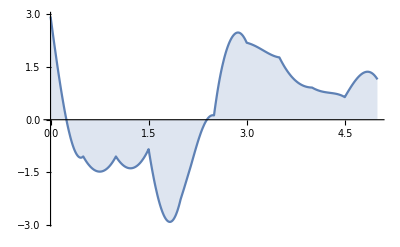
-Graphics-u(t)

```mathematica
p={-0.1,-0.2,-4,-3};
uFeedback[time_] := polePlacementFeedback[p,x1b[time],xdot1b[time],θ1b[time],θdot1b[time],x1a[time],xdot1a[time],θ1a[time],θdot1a[time],u1a[time],A]
Labeled[Plot[uFeedback[t],{t,0,τ},Filling->{1->Axis}],"u(t)"]
```

## Debugging Scripts

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
polePlacementFeedback[p_,xm_,xdotm_,θm_,θdotm_,xff_,xdotff_,θff_,θdotff_,uff_,A_] := Module[{fx,nDim,xState ,x,xdot,θ,θdot,x2dot,θ2dot,u,L,Af,Bf,Cf,ssm,K,uStar,uFinal,i,j},
nDim = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,nDim}];
Cf = {1,1,1,1};
x = xm - xff;xdot =  xdotm - xdotff;θ =  θm - θff;θdot =  θdotm - θdotff;u = uff; 

ssm = StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,nDim}],{i,1,nDim}],Table[Bf[[i]],{i,1,nDim}],Table[Table[Cf[[i]],{i,j,nDim}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None];
K = StateFeedbackGains[ssm,p];
uStar = -K.xState;
(*u = uff + uStart  *)
uFinal = u + uStar]
n = 10; τ = 5; τ1 = τ*1.25 ; A = 0.2; 
ICs = {0,0,0,0};
{xff0,xdotff0,θff0,θdotff0,uff0}=ffCartPendulum[ICs,n,τ,τ1,A];

κ1=κ2=3;  (* lqr for q=r for balancing pendulum *)
κ3 = -0.1;κ4 = -0.65;
p={-0.1,-0.2,-4,-3};
xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
u[t_]:=polePlacementFeedback[p,x[t],xdot[t],θ[t],θdot[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))};

init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};

{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NDSolveValue::underdet: There are more dependent variables, {InterpolatingFunction[{{0.,5.}},{5.,7.,0.,{11.},{2.},0.,0.,0.,0.,Automatic,«3»},{{0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,«1»}},{Developer`PackedArrayForm,{0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,«2»},{0.,-0.796011,-0.409414,0.1546,1.12502,1.83581,1.49645,1.05825,0.967821,0.710757,«1»}},{Automatic}][t],«5»,θdot[t]}, than equations, so the system is underdetermined.

Set::shape: Lists {xs,xdots,θs,θdots} and NDSolveValue[{{x'[t]==xdot[t],xdot'[t]=={(Piecewise[«2»]+Times[«3»]+Times[«3»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«4»])/Plus[«2»]},θ'[t]==θdot[t],θdot'[t]=={(Times[«2»]+Times[«3»])/Plus[«2»]}},{x[0]==0,xdot[0]==0,θ[0]==0,θdot[0]==0}},{x,xdot,θ,θdot},{t,0,6.25},Method→{DiscontinuityProcessing→None}] are not the same shape.

```mathematica
u[1]
```

{-0.0755672+x[1]+xdot[1]+θ[1]+θdot[1],-0.175567+x[1]+xdot[1]+θ[1]+θdot[1],-3.97557+x[1]+xdot[1]+θ[1]+θdot[1],-2.97557+x[1]+xdot[1]+θ[1]+θdot[1]}

```mathematica
x[1] = 0;
xdot[1] = 0;
θ[1] = 0;
θdot[1] = 0;
u[1]
```

{9.00715}

```mathematica
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];

us[t_]:=polePlacementFeedback[p,xs[t],xdots[t],θs[t],θdots[t],xff[t],xdotff[t],θff[t],θdotff[t],uff[t],A];

J = NIntegrate[us[t]^2,{t,0,τ}];

{xs,xdots,θs,θdots,us,J}
```

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
n = 4;
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,n}];
Cf = {1,1,1,1};
x = 1;xdot = 1;θ = 1;θdot = 0;A = 0.2;u = 0; 
p={-0.1,-0.2,-4,-3};
ssm = StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,n}],{i,1,n}],Table[Bf[[i]],{i,1,n}],Table[Table[Cf[[i]],{i,j,n}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None];
K = StateFeedbackGains[ssm,p];
uStar = -K.xState;
(*u = uff + uStart  *)
uFinal = u + uStar
```

{14.8333}

```mathematica
Clear["Global`*"]; 
Remove["Global`*"];
Af = {{a1,a2},{a3,a4}};n = 2;
Bf = {b1,b2};
Bf = Table[Table[Bf[[i]],{i,j,j}],{j,1,n}];
Cf = {c1,c2};
StateSpaceModel[{Table[Table[Af[[i]][[j]],{j,1,n}],{i,1,n}],Table[Bf[[i]],{i,1,n}],Table[Table[Cf[[i]],{i,j,n}],{j,1,1}]},SamplingPeriod->None,SystemsModelLabels->None]
```

a1a2b1a3a4b2c1c20StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNoneAutomatic

```mathematica
Cf = {c1,c2};
Cf =
```

{{1,1}}